## Some definitions

```mathematica
Clear[nodes];
```

```mathematica
PartitionHasTrianglePattern[sets_]:=Block[{result=False},
If[Length[sets]==4,
If[MemberQ[sets[[1]],1],
If[MemberQ[sets[[1]],3],
If[MemberQ[sets[[2]],2],
If[MemberQ[sets[[2]],4],
If[MemberQ[sets[[3]],5],
result=True
]
]
]
]
]
];
result
]
```

```mathematica
ComparePartitions[p1_,p2_]:=Block[{},
If[Length[p1]≠Length[p2],
Length[p1]>Length[p2],
If[Length[p1]==0,
False,
p1[[1]]<p2[[1]]
]
]
]
```

```mathematica
NormalizePartion[p_]:=Sort[p,Min[#1]<Min[#2]&]
```

```mathematica
RemoveLow[sets_]:=NormalizePartion[Map[Select[#,!MemberQ[{1,2,3,4,5},#]&]&,sets]]
```

## Now count the number of 4-partitions that have pattern 13|24|5|...

```mathematica
Clear[four];Clear[five];Clear[fiveprotect];Clear[fivedestruct]
```

```mathematica
four[nodes_]:=four[nodes]=Select[KSetPartitions[Range[nodes],4],PartitionHasTrianglePattern]
```

five is the 5-partitions of which the “four” are a refinement.

```mathematica
five[nodes_]:=five[nodes]=Sort[DeleteDuplicates[Flatten[Map[FindFiner,four[nodes]],1]]];
```

```mathematica
fiveprotect[nodes_]:=fiveprotect[nodes]=Select[five[nodes],
PartitionHasPattern[#,{{1,3},{2},{4},{5}}]||
PartitionHasPattern[#,{{1},{2,4},{3},{5}}]||
PartitionHasPattern[#,{{1},{2},{3,5},{4}}]||
PartitionHasPattern[#,{{1,4},{2},{3},{5}}]||
PartitionHasPattern[#,{{1},{2,5},{3},{4}}]
&];Length[fiveprotect]
```

0

```mathematica
fivedestruct[nodes_]:=fivedestruct[nodes]=SetDifference[five[nodes],fiveprotect[nodes]]//Sort;
```

```mathematica
Map[SetsToSymbol,fivedestruct[6]]
```

{v1x24x3x5x6,v13x2x4x5x6}

```mathematica
Monitor[TableForm[Table[
Table[
Sort[DeleteDuplicates[Select[Map[Select[#,#≠{}&]&,Map[RemoveLow,fivedestruct[nodes]]],Length[#]==l&]],ComparePartitions]//Length,
{l,1,nodes-5}
],
{nodes,6,11}]
,TableDepth->2],{nodes,l}]
```

$Aborted

```mathematica
TableForm[
Table[Tally[Map[Length[Select[#,#=={}&]]&,Map[RemoveLow,fivedestruct[nodes]]]],
{nodes,6,10}],
TableDepth->1]
```

{{4,2}}
{{4,2},{3,17}}
{{4,2},{3,51},{2,81}}
{{4,2},{3,119},{2,486},{1,228}}
{{4,2},{3,255},{2,2025},{1,2280},{0,300}}

```mathematica
TableForm[
Table[
Table[Length[Select[Map[Select[#,#≠{}&]&,Map[RemoveLow,fivedestruct[nodes]]],Length[#]==l&]],{l,1,nodes-5}],
{nodes,6,10}],
TableDepth->1]
```

{0}
{0,1}
{0,3,9}
{0,7,54,36}
{0,15,225,360,60}

## Visualizaing everything

```mathematica
Map[SetsToSymbol,fivedestruct[6]]
```

{}

```mathematica
Map[SetsToSymbol,KSetPartitions[6,4]]
```

{v1x2x3x456,v1x2x34x56,v1x2x356x4,v1x2x345x6,v1x2x36x45,v1x2x346x5,v1x2x35x46,v1x23x4x56,v1x24x3x56,v1x256x3x4,v1x23x45x6,v1x245x3x6,v1x26x3x45,v1x23x46x5,v1x246x3x5,v1x25x3x46,v1x234x5x6,v1x25x34x6,v1x26x34x5,v1x235x4x6,v1x24x35x6,v1x26x35x4,v1x236x4x5,v1x24x36x5,v1x25x36x4,v12x3x4x56,v13x2x4x56,v14x2x3x56,v156x2x3x4,v12x3x45x6,v13x2x45x6,v145x2x3x6,v16x2x3x45,v12x3x46x5,v13x2x46x5,v146x2x3x5,v15x2x3x46,v12x34x5x6,v134x2x5x6,v15x2x34x6,v16x2x34x5,v12x35x4x6,v135x2x4x6,v14x2x35x6,v16x2x35x4,v12x36x4x5,v136x2x4x5,v14x2x36x5,v15x2x36x4,v123x4x5x6,v14x23x5x6,v15x23x4x6,v16x23x4x5,v124x3x5x6,v13x24x5x6,v15x24x3x6,v16x24x3x5,v125x3x4x6,v13x25x4x6,v14x25x3x6,v16x25x3x4,v126x3x4x5,v13x26x4x5,v14x26x3x5,v15x26x3x4}

```mathematica
Map[SetsToSymbol,five[6]]
```

{v1x24x3x5x6,v13x2x4x5x6}

```mathematica
Map[SetsToSymbol,fiveprotect[6]]
```

{v1x24x3x5x6,v13x2x4x5x6}

```mathematica
Join[Map[SetsToSymbol,KSetPartitions[6,4]],Map[SetsToSymbol,KSetPartitions[6,5]]]
```

{v1x2x3x456,v1x2x34x56,v1x2x356x4,v1x2x345x6,v1x2x36x45,v1x2x346x5,v1x2x35x46,v1x23x4x56,v1x24x3x56,v1x256x3x4,v1x23x45x6,v1x245x3x6,v1x26x3x45,v1x23x46x5,v1x246x3x5,v1x25x3x46,v1x234x5x6,v1x25x34x6,v1x26x34x5,v1x235x4x6,v1x24x35x6,v1x26x35x4,v1x236x4x5,v1x24x36x5,v1x25x36x4,v12x3x4x56,v13x2x4x56,v14x2x3x56,v156x2x3x4,v12x3x45x6,v13x2x45x6,v145x2x3x6,v16x2x3x45,v12x3x46x5,v13x2x46x5,v146x2x3x5,v15x2x3x46,v12x34x5x6,v134x2x5x6,v15x2x34x6,v16x2x34x5,v12x35x4x6,v135x2x4x6,v14x2x35x6,v16x2x35x4,v12x36x4x5,v136x2x4x5,v14x2x36x5,v15x2x36x4,v123x4x5x6,v14x23x5x6,v15x23x4x6,v16x23x4x5,v124x3x5x6,v13x24x5x6,v15x24x3x6,v16x24x3x5,v125x3x4x6,v13x25x4x6,v14x25x3x6,v16x25x3x4,v126x3x4x5,v13x26x4x5,v14x26x3x5,v15x26x3x4,v1x2x3x4x56,v1x2x3x45x6,v1x2x3x46x5,v1x2x34x5x6,v1x2x35x4x6,v1x2x36x4x5,v1x23x4x5x6,v1x24x3x5x6,v1x25x3x4x6,v1x26x3x4x5,v12x3x4x5x6,v13x2x4x5x6,v14x2x3x5x6,v15x2x3x4x6,v16x2x3x4x5}

```mathematica
FormulaGraphReverse2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel[ SetsToSymbol[s]],Pi/3],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

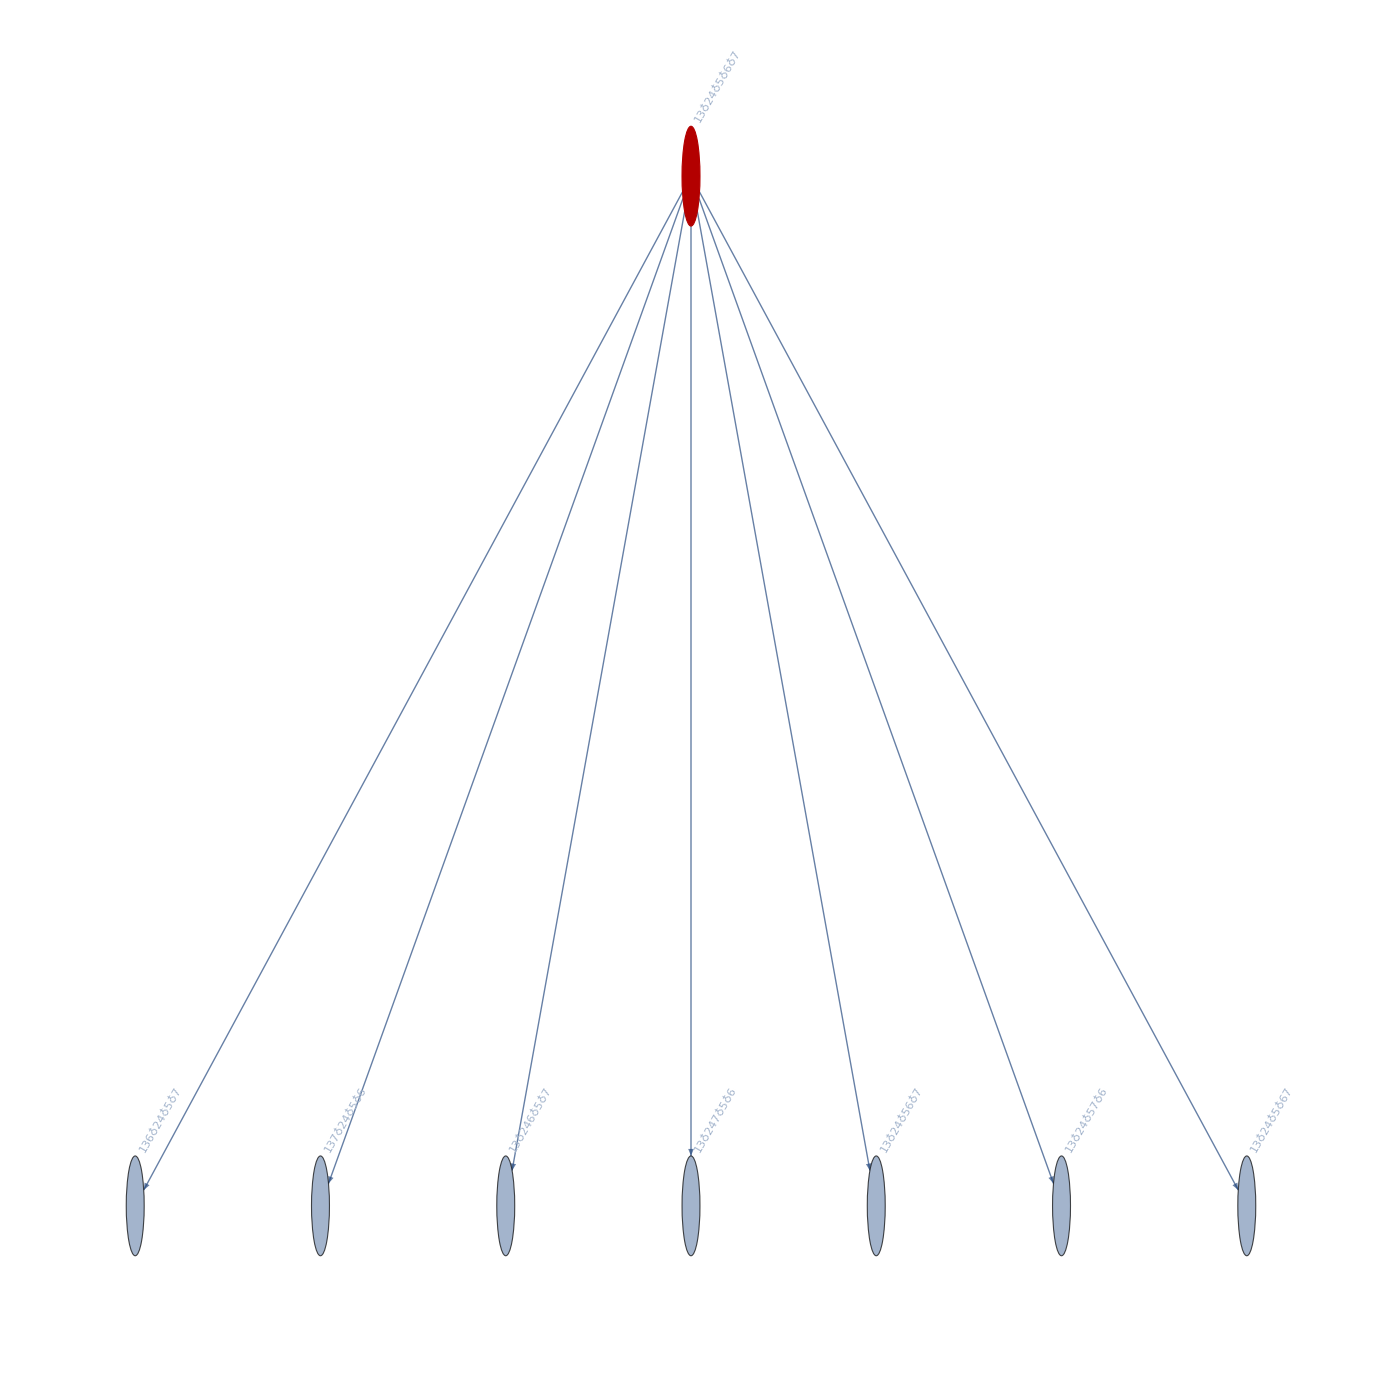

```mathematica
With[
{size=7},
Graph[FormulaGraphReverse2[Map[SetsToSymbol,Join[four[size],fivedestruct[size]]]],GraphHighlight->Map[SetsToSymbol,fivedestruct[size]]]
]
```